# Homework 17

## Problem 17.1

1. A small bar of soap with mass m = 125 g is placed in a bowl of hemispherical shape. The soap can slide without friction on the surface of the bowl. The radius of curvature of the bowl is R=50.0 cm. Use a coordinate system where the z axis points upward. (Thus, when the soap is in the bottom of the bowl theta  = Pi .) Let the bar of soap be initally at an angle of  = 5 π/6 (30 degrees up from the bottom of the bowl), be moving up the bowl (theta direction) with a velocity of 2.00 m/s, and be moving around the bowl (ϕ direction) with a velocity of 1.00 m/s.
Solve the system.
Note: We solved a very similar problem back in Homework 9 using traditional conservation of energy techniques. Now we get to do it again with Lagrangian techniques.

```mathematica
Quit[]
```

```mathematica
Clear["'*"]
```

Let the velocity in the theta direction be vtheta and the phi direction be vphi. Use geometry to express vtheta and vphi in terms of R, theta, thetadot, phi, and phidot (you won’t need all of these quantities). Given that vtheta and vphi are perpendicular to each other, think about how you can include them in the total kinetic energy. Then express T and U in terms of R, theta, thetadot, phi, and phidot.

```mathematica
vtheta=R*thetadot;
vphi=phidot*R*Cos[theta-Pi/2];
T=(1/2)*m*(vtheta^2+vphi^2)
U=m*g*R*Cos[theta]
L=T-U
```

1/2 m (R^2 thetadot^2+phidot^2 R^2 Sin[theta]^2)

g m R Cos[theta]

-g m R Cos[theta]+1/2 m (R^2 thetadot^2+phidot^2 R^2 Sin[theta]^2)

### Having trouble with T and U?

There are θ and ϕ components of the velocity.  These are perpendicular to each other and independent.  We know that v=r*ω, but we have to be careful about what r to use.  For the θ direction, this is R, and for the ϕ direction, it is R*Sin[θ].  Why?

Thus:
T=1/2 m R^2 θdot^2+1/2 m R^2 ϕdot^2 Sin[θ]^2

For U, we just have U=m*g*z=m*g*R*Cos[θ]

Alternative approach for T: Just define x, y, and z in terms of r, theta, and phi using the usual spherical coordinates. Then you can calculate xdot, ydot, and zdot, remembering that r has no time dependence (because the soap is constrained to be on the surface of the sphere, which has constant radius). Then T = 1/2 m (xdot^2+ydot^2+zdot^2).

From Homework 16, you know how to proceed from here. After calculating the various derivatives, use the replacement rule given below to put the expressions in the proper form for differentiation in Mathematica. The usage is as follows: D[“????”,”????”]/.rule

```mathematica
rule = {theta->theta[t],thetadot->theta'[t],phi->phi[t],phidot->phi'[t]}
dLdtheta=D[L,theta]/.rule;
dLdthetadot=D[L,thetadot]/.rule;
dLdphi=D[L,phi]/.rule;
dLdphidot=D[L,phidot]/.rule;
```

{theta→theta[t],thetadot→theta'[t],phi→phi[t],phidot→phi'[t]}

```mathematica
θeq=dLdtheta==D[dLdthetadot,t]
ϕeq=dLdphi==D[dLdphidot,t]
```

g m R Sin[theta[t]]+m R^2 Cos[theta[t]] Sin[theta[t]] phi'[t]^2==m R^2 theta''[t]

0==2 m R^2 Cos[theta[t]] Sin[theta[t]] phi'[t] theta'[t]+m R^2 Sin[theta[t]]^2 phi''[t]

Plug in numerical values and initial conditions. Be careful with the initial angular velocities θdot0 and ϕdot0 (they are NOT just 2 m/s and 1 m/s! There is one more step you have to take to get these angular velocities.).

```mathematica
m=0.125;
R=.5;
g=9.8;
θ0=(5π)/6;
θdot0=2/R;
ϕdot0=1/(R*Cos[θ0-Pi/2]);
```

### Having trouble with the initial conditions?

The boundary conditions in θdot and ϕdot are :
 v_ 0 _θ = R*θdot0
v_ 0 _ϕ = R*sin [θ0]*ϕdot0

Why?

Now solve and enjoy some pretty pictures!

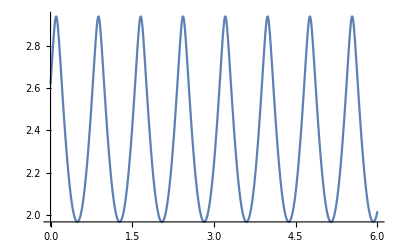

```mathematica
bc={theta[0]==θ0,phi[0]==0,theta'[0]==θdot0,phi'[0]==ϕdot0};
sol1=NDSolve[{θeq,ϕeq,bc},{theta,phi},{t,0,6}];
Plot[Evaluate[theta[t]/.sol1],{t,0,6}]
```

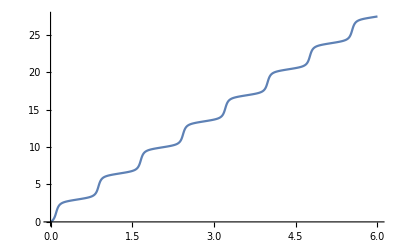

```mathematica
Plot[Evaluate[phi[t]/.sol1],{t,0,6}]
```

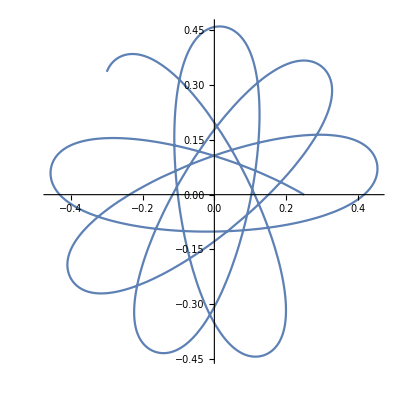

```mathematica
ParametricPlot[Evaluate[{R*Sin[theta[t]]*Cos[phi[t]],R*Sin[theta[t]]*Sin[phi[t]]}/.sol1],{t,0,6}]
```

```mathematica
ParametricPlot3D[Evaluate[{R*Sin[theta[t]]*Cos[phi[t]],R*Sin[theta[t]]*Sin[phi[t]],R*(1+Cos[theta[t]])}/.sol1],{t,0,6}]
```

-Graphics3D-

## Problem 17.2

A block off mass M slides frictionlessly on an air table. On top of the block is a post that supports a pendulum of length d and mass m. Make a plot of the motion of the cart if the pendulum is raised to an angle theta and released from rest.

Use the following values:
     M=1.24 kg
     m=150 kg
     d=0.300 m
     theta0=60 degrees

Call the coordinate of the block X  with X=0 initially.
Call the coordinates of the pendulum x and y as measured with respect to equilibrium (theta=0) position of the pendulum.

Repeat the calculation for theta0=175 degrees.
See if you can understand the motion of the system. (Hint: What quantity is conserved?)

```mathematica
Quit[]
```

```mathematica
Clear["'*"]
```

(A) Find the kinetic and potential energies of the system. We may conveniently do this in steps.

Find x(t) and y(t) in terms of X(t) and theta(t).  -- Use this notation!

```mathematica
x[t]=X[t]+d*Sin[theta[t]];
y[t]=d-d*Cos[theta[t]]
D[x[t],t]
D[y[t],t]
```

d-d Cos[theta[t]]

d Cos[theta[t]] theta'[t]+X'[t]

d Sin[theta[t]] theta'[t]

### Solution

```mathematica
x$[t]=X[t]+d*Sin[theta[t]];
y$[t]=d*(1-Cos[theta[t]]);
If[FullSimplify[Solve[x[t]==x$[t],d]]=={{}},Print["x[t] is correct"],Print["x[t]=X[t]+d*Sin[theta[t]]"]]
If[FullSimplify[Solve[y[t]==y$[t],d]]=={{}},Print["y[t] is correct"],Print["y[t]=d*(1-Cos[theta[t]])"]]
```

x[t] is correct

y[t] is correct

Use dX/dt=Xdot and dtheta/dt=thetadot. Let increasing theta be defined so that when thetadot is positive, the pendulum is moving in the positive x direction. This time, just write theta, not theta(t), as we want T and U to be functions of theta, thetadot, X, and Xdot only.

```mathematica
T=(1/2)*M*Xdot^2+(1/2)*m*(Xdot+d*Cos[theta]*thetadot)^2+(1/2)*m*(d*Sin[theta]*thetadot)^2;
U=m*g*d*(1-Cos[theta]);
L=T-U;
```

### Solutions

```mathematica
T$=M/2*Xdot^2+m/2*(Xdot+d*Cos[theta]*thetadot)^2+m/2*(d*Sin[theta]*thetadot)^2;
U$=m*g*d*(1-Cos[theta]);
If[FullSimplify[Solve[T==T$,m]]=={{}},Print["T is correct"],Print["Check your T"]]
If[FullSimplify[Solve[U==U$,m]]=={{}},Print["U is correct"],Print["Check your U"]]
```

T is correct

U is correct

Take derivatives and find the equations of motion. Be sure that t dependence is explicit in every reference to X and theta.

```mathematica
rule={X->X[t],Xdot->X'[t],theta->theta[t],thetadot->theta'[t]};
dLdX=D[L,X]/.rule;
dLdXdot=D[L,Xdot]/.rule;
dLdtheta=D[L,theta]/.rule;
dLdthetadot=D[L,thetadot]/.rule;
```

```mathematica
eqX=dLdX==D[dLdXdot,t]
```

0==M X''[t]+m (-d Sin[theta[t]] theta'[t]^2+d Cos[theta[t]] theta''[t]+X''[t])

```mathematica
eqθ=dLdtheta==D[dLdthetadot,t]
```

-d g m Sin[theta[t]]+d^2 m Cos[theta[t]] Sin[theta[t]] theta'[t]^2-d m Sin[theta[t]] theta'[t] (d Cos[theta[t]] theta'[t]+X'[t])==2 d^2 m Cos[theta[t]] Sin[theta[t]] theta'[t]^2-d m Sin[theta[t]] theta'[t] (d Cos[theta[t]] theta'[t]+X'[t])+d^2 m Sin[theta[t]]^2 theta''[t]+d m Cos[theta[t]] (-d Sin[theta[t]] theta'[t]^2+d Cos[theta[t]] theta''[t]+X''[t])

### Want to check your equations?

eqX=D[M*D[X[t],t]+m*(D[X[t],t]+d*Cos[θ[t]]*D[θ[t],t]),t]==0
eqθ=-m*(D[X[t],t]+d*Cos[θ[t]]*D[θ[t],t])*d*Sin[θ[t]]*D[θ[t],t]+m*d^2*Sin[θ[t]]*D[θ[t],t]^2*Cos[θ[t]]-m*g*d*Sin[θ[t]]==
	D[m*(D[X[t],t]+d*Cos[θ[t]]*D[θ[t],t])*d*Cos[θ[t]]+m*d^2*Sin[θ[t]]^2*D[θ[t],t],t]

Numerical values :

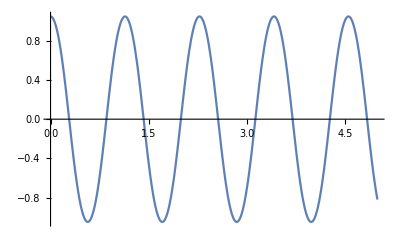

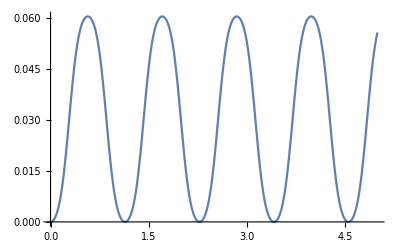

```mathematica
M=1.14;
m=.150;
d=.3;
g=9.8;
θ0=π/3;
bc={X[0]==0,theta[0]==θ0,X'[0]==0,theta'[0]==0};
sol1=NDSolve[{eqX,eqθ,bc},{theta,X},{t,0,5}];
Plot[Evaluate[theta[t]/.sol1],{t,0,5}]
Plot[Evaluate[X[t]/.sol1],{t,0,5}]
```

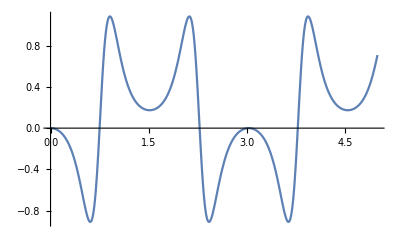

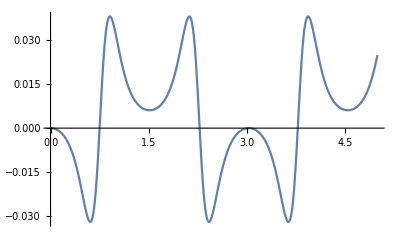

```mathematica
θ0=π*175/180;
bc={X[0]==0,theta[0]==θ0,X'[0]==0,theta'[0]==0};
sol2=NDSolve[{eqX,eqθ,bc},{theta,X},{t,0,5}];
Plot[Evaluate[(X[t]/(.035))/.sol2],{t,0,5}]
Plot[Evaluate[X[t]/.sol2],{t,0,5}]
```

This is just a little something to play around with and see how X[t] and θ[t] change as θ0 varies from 0 to 2π.

```mathematica
Animate[Plot[Evaluate[theta[t]/.NDSolve[{eqX,eqθ,X[0]==0,theta[0]==θ0,X'[0]==0,theta'[0]==0},{theta,X},{t,0,5}]],{t,0,5}],{θ0,0,2π}]
Animate[Plot[Evaluate[X[t]/.NDSolve[{eqX,eqθ,X[0]==0,theta[0]==θ0,X'[0]==0,theta'[0]==0},{theta,X},{t,0,5}]],{t,0,5}],{θ0,0,2π}]
```

## Written Problems

-Graphics-